# Versuch 39

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

```mathematica
f[{a_,b_}]:=TeXForm@NumberForm[SetAccuracy[a±b,Accuracy@SetPrecision[b,2]],ExponentFunction->(Null&)]//ToString//Quiet
```

## Import Data

```mathematica
rawDataLangsam=Import[NotebookDirectory[]<>"Holzkern langam, 2mVs messbereich.txt"];
rawDataSchnell=Import[NotebookDirectory[]<>"Holzkern schnell, 2mVs messbereich.txt"];
```

```mathematica
dataLangsam=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[rawDataLangsam,"\n"],"	"]]][[2;;]];
dataLangsam=Map[ToExpression,dataLangsam,{2}];
dataSchnell=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[rawDataSchnell,"\n"],"	"]]][[2;;]];
dataSchnell=Map[ToExpression,dataSchnell,{2}];
```

```mathematica
cols1=ColorData["M10DefaultDensityGradient"]/@Rescale[dataLangsam[[All,1]], {Min[dataLangsam[[All,1]]],Max[dataLangsam[[All,1]]]}];
cols2=ColorData["M10DefaultDensityGradient"]/@Rescale[dataSchnell[[All,1]], {Min[dataLangsam[[All,1]]],Max[dataLangsam[[All,1]]]}];
```

## Parameters

```mathematica
da=260*10^(-3);
di=220*10^(-3);
h=30*10^(-3);
```

```mathematica
N1=1010;
d=(da+di)/2;
R=67.8;
```

```mathematica
N2=250;
A=h (da-di)/2;
messbereich=2;
fullfaktor=1;
```

```mathematica
dataProcessedSchnell={N1 #[[1]]/(π d R),(messbereich/1000)((#1⟦2⟧)/(N2 fullfaktor A))}&/@dataSchnell[[All,{2,3}]];
dataProcessedLangsam={N1 #[[1]]/(π d R),(messbereich/1000)((#1⟦2⟧)/(N2 fullfaktor A))}&/@dataLangsam[[All,{2,3}]];
```

```mathematica
Show[ListPlot[List/@dataProcessedLangsam,PlotStyle->cols1,PlotLegends->BarLegend[{ColorData["M10DefaultDensityGradient"],{Min[dataLangsam[[All,1]]],Max[dataLangsam[[All,1]]]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}],pltsettings],ListPlot[List/@dataProcessedSchnell,PlotStyle->cols2]]//Rasterize
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"abbildungen/holzkern raw.pdf",Show[ListPlot[{{#[[1]],#[[2]]*10^3}}&/@dataProcessedLangsam,PlotStyle->cols1,PlotLegends->BarLegend[{ColorData["M10DefaultDensityGradient"],{Min[dataLangsam[[All,1]]],Max[dataLangsam[[All,1]]]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}],pltsettings],ListPlot[{{#[[1]],#[[2]]*10^3}}&/@dataProcessedSchnell,PlotStyle->cols2]],Background->None];
```

## Regression with pure measurement

```mathematica
dataDrift=Import[NotebookDirectory[]<>"Nullpunktdrift mit Holzkern 1.txt"];
dataDrift=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[dataDrift,"\n"],"	"]]][[2;;]];
dataDrift=Map[ToExpression,dataDrift,{2}];
```

```mathematica
dataProcessedDrift={N1 #[[1]]/(π d R),(messbereich/1000)((#1⟦2⟧)/(N2 fullfaktor A))}&/@dataDrift[[All,{2,3}]];
```

```mathematica
linregdata=Transpose[{dataDrift[[All,1]],dataProcessedDrift[[All,2]]}];
```

```mathematica
fit=LinearModelFit[linregdata,x,x]
```

FittedModel[…]

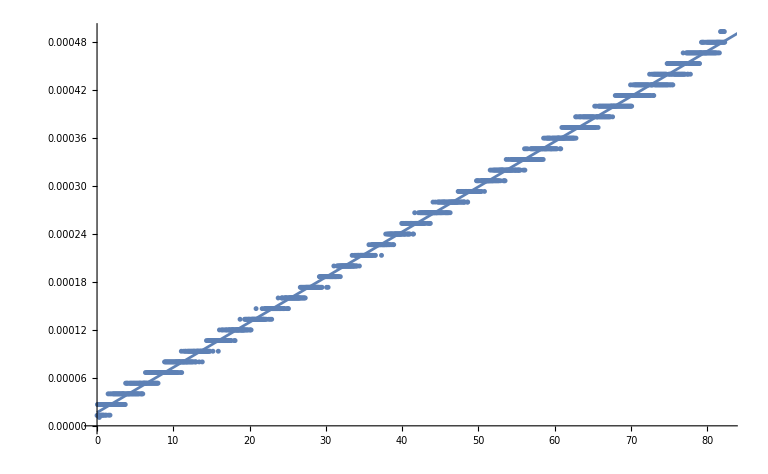

```mathematica
Show[ListPlot[linregdata],Plot[fit[x],{x,0,90}]]
```

```mathematica
correctedLangsam=Table[{dataProcessedLangsam[[i,1]],dataProcessedLangsam[[i,2]]-5.650270138118802*^-6 dataLangsam[[i,1]]},{i,1,Length[dataLangsam]}];
```

```mathematica
correctedSchnell=Table[{dataProcessedSchnell[[i,1]],dataProcessedSchnell[[i,2]]-5.650270138118802*^-6dataSchnell[[i,1]]},{i,1,Length[dataSchnell]}];
```

```mathematica
ListPlot[List/@correctedSchnell,PlotStyle->cols2]//Rasterize
```

-Graphics-

```mathematica
ListPlot[List/@correctedLangsam,PlotStyle->cols1]//Rasterize
```

-Graphics-

## Linear Fit Through Endpoint

```mathematica
dataProcessedSchnell[[-100;;-1,2]]
```

{0.000906667,0.000893333,0.000893333,0.000893333,0.000893333,0.000893333,0.000893333,0.000893333,0.000893333,0.000893333,0.00088,0.000893333,0.000893333,0.000893333,0.000893333,0.000893333,0.000893333,0.000893333,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.000866667,0.000866667,0.000866667,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.00088,0.000893333,0.00088,0.00088,0.00088,0.000893333,0.00088,0.000893333,0.00222667,0.00294667,0.00294667,0.00296,0.00294667,0.00296,0.00296,0.00296,0.00296,0.00296,0.00294667,0.00296,0.00294667,0.00296,0.00296,0.00296,0.00296}

```mathematica
startpt1=dataProcessedSchnell[[1,2]]
```

-5.5×10^-6

```mathematica
startpt2=dataProcessedLangsam[[1,2]]
```

-0.00004

```mathematica
endpt1=dataProcessedSchnell[[-18,2]]
```

0.000893333

```mathematica
endpt2=dataProcessedLangsam[[-1,2]]
```

0.00241333

```mathematica
dataProcessedLangsam[[-1,2]]
```

0.00241333

```mathematica
t1=dataSchnell[[-18,1]]
t2=dataLangsam[[-1,1]]
```

149.2

424.85

```mathematica
grad=(endpt2-(endpt1+(startpt2-startpt1)))/(t2-t1)
```

5.6394×10^-6

```mathematica
correctedSchnell2=Table[{dataProcessedSchnell[[i,1]],dataProcessedSchnell[[i,2]]-grad dataSchnell[[i,1]]},{i,1,Length[dataSchnell]}];
```

```mathematica
ListPlot[correctedLangsam2]
```

ListPlot::lpn: correctedLangsam2 is not a list of numbers or pairs of numbers.

ListPlot[correctedLangsam2]

```mathematica
correctedLangsam2=Table[{dataProcessedLangsam[[i,1]],dataProcessedLangsam[[i,2]]-grad dataLangsam[[i,1]]},{i,1,Length[dataLangsam]}];
```

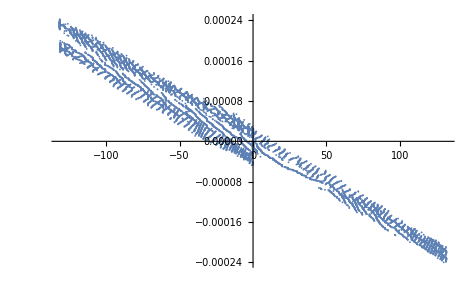

```mathematica
ListPlot[correctedLangsam2]
```

## Just Fitting it

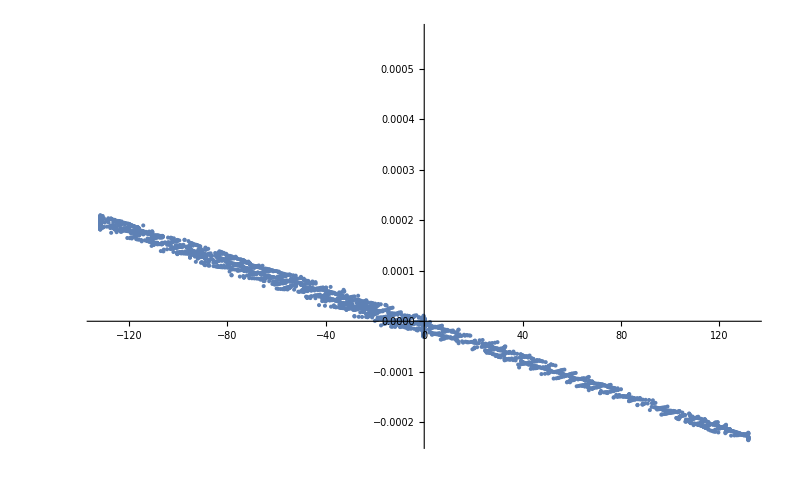

```mathematica
correctedSchnell3=Table[{dataProcessedSchnell[[i,1]],dataProcessedSchnell[[i,2]]-6.1*10^(-6) dataSchnell[[i,1]]},{i,1,Length[dataSchnell]}];
ListPlot[correctedSchnell3]
```

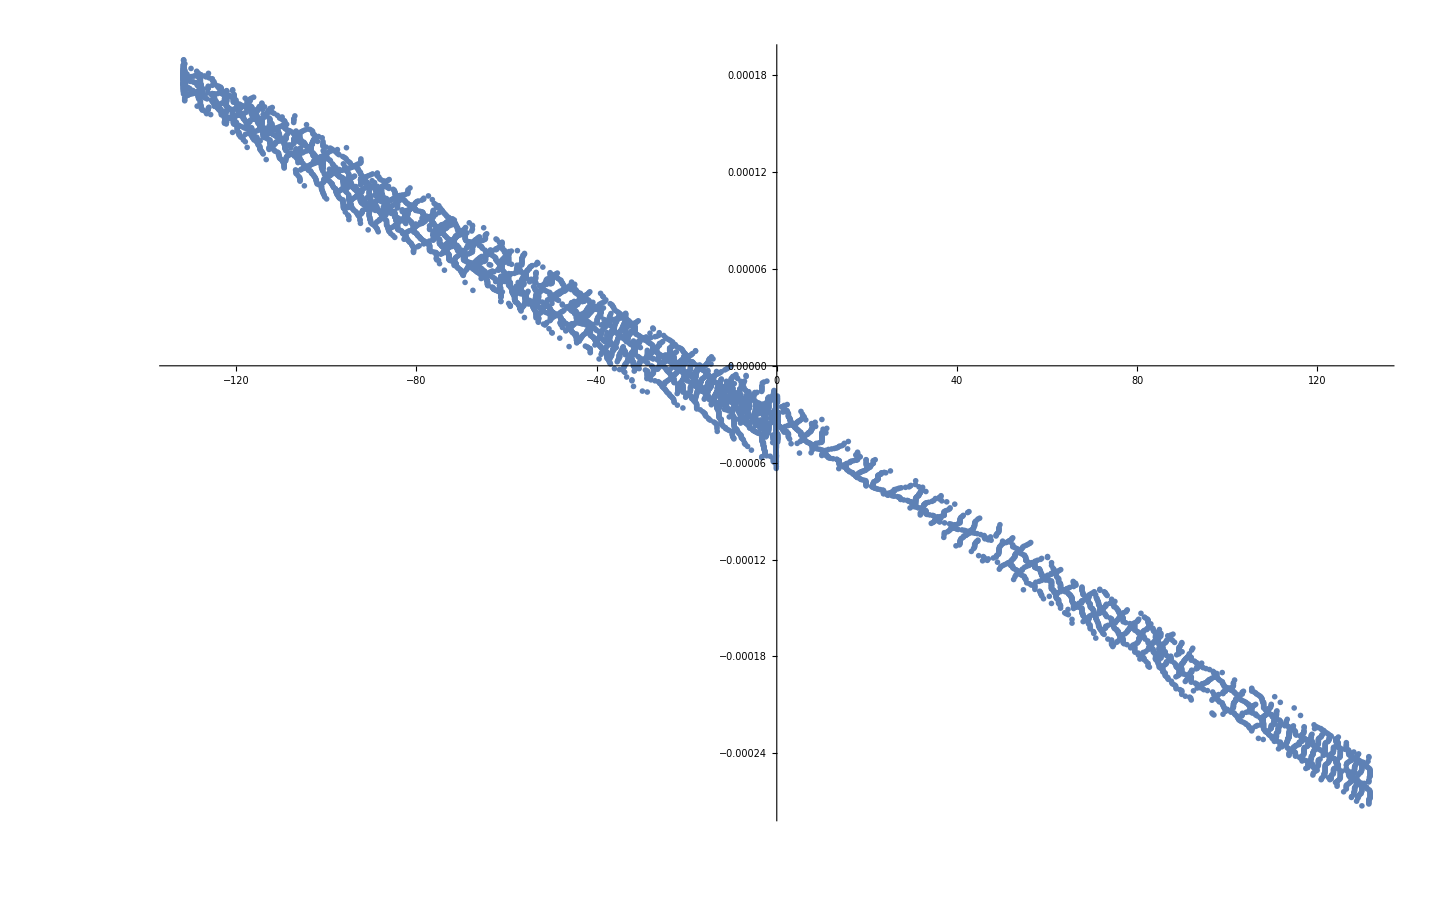

```mathematica
correctedLangsam3=Table[{dataProcessedLangsam[[i,1]],dataProcessedLangsam[[i,2]]-5.8*10^(-6) dataLangsam[[i,1]]},{i,1,Length[dataLangsam]}];
ListPlot[correctedLangsam3]
```

## Everything else with correctedSchnell3

```mathematica
correctedData={#[[1]], -#[[2]]}&/@correctedSchnell3
```

```mathematica
LinearModelFit[correctedData,x,x]
```

FittedModel[…]

```mathematica
LinearModelFit[correctedData,x,x]["ParameterTable"]
```

General::munfl: Exp[-776.119] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.69098×10^-6 | 2.83052×10^-6 | 0.597409 | 0.550279
x | 1.59802×10^-6 | 3.55521×10^-8 | 44.9488 | 0.

```mathematica
(4.71393×10^-9)/(4π*10^(-7))
```

0.00375123

```mathematica
Min[correctedData[[All,1]]]
Max[correctedData[[All,1]]]
Min[correctedData[[All,2]]]
Max[correctedData[[All,2]]]
```

-131.743

131.762

-0.00204866

0.000235277

```mathematica
Sort[correctedData[[All,2]]][[1;;20]]
```

{-0.00204866,-0.00204805,-0.00204775,-0.00204744,-0.00204714,-0.00204683,-0.00204622,-0.00204561,-0.00204531,-0.002045,-0.0020447,-0.00203594,-0.00203563,-0.00203502,-0.00203319,-0.00203258,-0.00131624,-0.000209832,-0.000208525,-0.000208283}

```mathematica
SortBy[correctedData,Last][[18,2]]
```

-0.000209832

```mathematica
shiftx=(Min[correctedData[[All,1]]]+Max[correctedData[[All,1]]])/2
shifty=(SortBy[correctedData,Last][[18,2]]+Max[correctedData[[All,2]]])/2
```

0.00987872

0.0000127225

```mathematica
finalData={#[[1]]-shiftx,#[[2]]-shifty}&/@correctedData;
```

```mathematica
pars=ungewichteterReg[finalData[[All,1]],finalData[[All,2]]]
```

{-0.0000110157,1.59802×10^-6,2.8306×10^-6,3.55521×10^-8}

```mathematica
pars[[2]]/(4π*10^(-7))
pars[[4]]/(4π*10^(-7))
```

1.27167

0.0282914

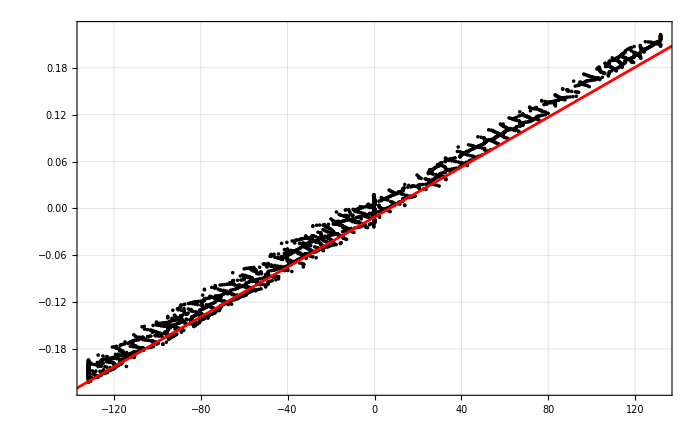

```mathematica
Show[ListPlot[{#[[1]],#[[2]]*10^3}&/@finalData,pltsettings,PlotRange->{All,{-0.00023*10^3,0.00023*10^3}},PlotStyle->Black],Plot[10^3(pars[[1]]+pars[[2]]x),{x,-200,200},PlotStyle->Red]]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/holzkern plot raw.pdf",Show[ListPlot[{#[[1]],#[[2]]*10^3}&/@finalData,pltsettings,PlotRange->{All,{-0.00023*10^3,0.00023*10^3}},PlotStyle->Black],Plot[10^3(pars[[1]]+pars[[2]]x),{x,-200,200},PlotStyle->Red]],Background->None];
```